## Muonium Antimatter Gravity Interferometry Code

This code is used to calculate intensity distributions of a muonium beam that passes through 2 grating structures. Ana Soter’s version used a completely uniform grating structure. This has been modified to also account for a grating structure with 50 nm wide slits separated by distances that alternate around 50 nm according to an adjustable offset. A notebook containing more detailed notes about the construction of this grating structure can be found on the drive: Fall 2021 Optics, “New grating coefficients by Alyssa.nb”

thickness of grating along z (how deep each grating is) <- not accounted for in code
wideness of beam is currently thin...should be thick
account for parameter: curvature of beam

run code and analyze simulTion results
compare bnetween the two variations what is  missing

question why it needs to be optimized

what is modelling doing?
transferring dsscription to fourier space
assumes grating is simple modification of beam in fourier space

start thinking about what other things the grating is affecting in fourier space

scattering function of beam in fourier space?

channeling of atom through small aperture -- hydrogen interaction with silicon nitride
wavelength = .6nm

grating is 1000x thicker than wavelength

waveguide effect of wave representations of atoms

matter v light waveguide theory^

```mathematica
(* Based on PhD thesis of McMorran *)

tbefore = TimeUsed[]; 

(* Toggle full plot on or off and swicth between grating structures *)
ShowFullPlot = False; (* Set to True to show intensity along entire z range, False to just show at final position*)
OriginalGrating = False; (* True to use Soter's uniform grating, false to use our grating coefficients with alternating separation between slits *)

(* adjust nonuniform grating structure *)
(*!!DO NOT set centeroffset more than + or - 25 nm!! slits will overlap and some of the open space will be double counted in calculation of fourier componenets so they will no longer be valid unless you manually change the limits of the sums *)
centeroffset = -15*10^(-9); (* use to adjust nonuniform grating (only used if OriginalGrating = False) offset of the center of the middle slit, -5*10^(-9) gives 5 nm to the left - we can adjust the severity of the imperfection here - 0 will give the same results as the uniform grating *)

(* Beam parameters *)

w0=1*10^-3; (*initial beam width, adjust this to match x-ray aperture *)
r0= -999999999999999999999; (*initial radius of wavefront curvature *)
ell0= w0;(* initial transverse coherence width *)
lambda=  0.56*10^(-9)(*with Mu: 0.58*10^-9;*) 

(* Grating parameters *)

d=1*10^-7; (*period of grating used if OriginalGrating = True *)
LT= d^2/lambda; (*Talbot length*)
NZ = Floor[20*10^-3/LT];
nu1=.5; (*grating 1 open fraction *)
nu2=.5; (*grating 2 open fraction *)
Z1=5*10^-3 ; (* position of grating 1, 5 mm along z axis *)
Z2=Z1+0.05 (*Z1+NZ*LT;*) (* position of grating 2, you can adjust the spacing between the gratings here, currently 5 cm to match x-ray *)
Z3 = Z2+(Z2-Z1); (* position of grating 3, all are equally spaced *)
X2=0;  (*initial offset of G2*)
theta=0;(*twist between gratings, in degrees*)

(* Limits of the plot *)

Zmin= 1*10^-3;(*1*10^-3;*)
Zmax= Z3+ 0.5*Z1;(*1*10^-3;*) (*the full plot goes slightly beyond the position of the third grating*)
Xmin=-4*10^(-3);(*-5000*d*) (*-400*d*) (* min and max x values of the plot, adjust these to zoom in/out *)
Xmax=4*10^(-3)(*5000*d*) (*1900*d*)

xpoints=500;(*resolution in the x direction*)
zpoints=500;(*resolution in the z direction*)

dZ=(Zmax-Zmin)/zpoints;(*step resolution used in computation*)
dX=(Xmax-Xmin)/xpoints;(*step resolution used in computation*)

image = True;(*switch to turn on or off the effects of image charges on an electron beam*)

xticks = {{1,Zmin},{1+0.2*(Zmax-Zmin)/dZ,Zmin+0.2*(Zmax-Zmin)},{1+0.4*(Zmax-Zmin)/dZ,Zmin+0.4*(Zmax-Zmin)}, {1+0.6*(Zmax-Zmin)/dZ,Zmin+0.6*(Zmax-Zmin)} , {1+0.8*(Zmax-Zmin)/dZ,Zmin+0.8*(Zmax-Zmin)},{1+(Zmax-Zmin)/dZ,Zmax}} ;
(*yticks = {{1,Xmin},{1+0.25*(Xmax-Xmin)/dX,Xmin+0.25*(Xmax-Xmin)},{1+0.5*(Xmax-Xmin)/dX,Xmin+0.5*(Xmax-Xmin)},{1+0.75*(Xmax-Xmin)/dX,Xmin+0.75*(Xmax-Xmin)},  {1+(Xmax-Xmin)/dX,Xmax}} ;*)
yticks = {{1,Xmin},{1+0.25*(Xmax-Xmin)/dX,Xmin+0.25*(Xmax-Xmin)},{1+0.5*(Xmax-Xmin)/dX,Xmin+0.5*(Xmax-Xmin)},{1+0.75*(Xmax-Xmin)/dX,Xmin+0.75*(Xmax-Xmin)},  {1+(Xmax-Xmin)/dX,Xmax}} ; (* these are used for the final plot, where the Z values are graphed on the x axis and the X values are on the y axis*)
```

5.6×10^-10

0.055

1/250

### Grating Fourier Components

(-20 | -2.95541×10^-16
-19 | -0.0451105
-18 | 0.0137662
-17 | -0.0313134
-16 | -7.52731×10^-17
-15 | 0.00928826
-14 | -0.0883968
-13 | 0.000315647
-12 | -2.71561×10^-16
-11 | -0.0217123
-10 | 0.0646567
-9 | -0.0720902
-8 | -4.55191×10^-17
-7 | 0.127709
-6 | -0.00488389
-5 | 0.15419
-4 | -2.30371×10^-16
-3 | -0.127277
-2 | 0.504597
-1 | -0.0493853
0 | 1.
1 | -0.0493853
2 | 0.504597
3 | -0.127277
4 | -2.30371×10^-16
5 | 0.15419
6 | -0.00488389
7 | 0.127709
8 | -4.55191×10^-17
9 | -0.0720902
10 | 0.0646567
11 | -0.0217123
12 | -2.71561×10^-16
13 | 0.000315647
14 | -0.0883968
15 | 0.00928826
16 | -7.52731×10^-17
17 | -0.0313134
18 | 0.0137662
19 | -0.0451105
20 | -2.95541×10^-16)

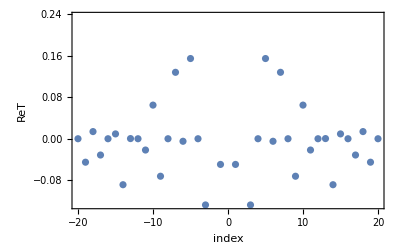

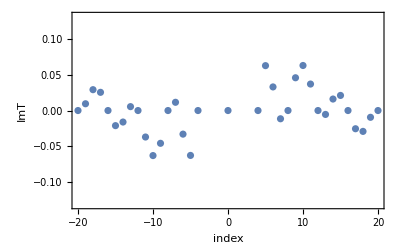

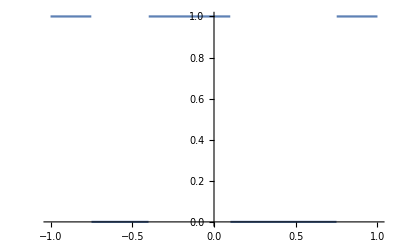

```mathematica
If[OriginalGrating,{
(*Soter's calculation of grating coefficients*)
(*defining grating parameters*)
width=nu2*d; (* width given by open fraction of grating 2 times the period of the grating, total open width of a single slit*)
thick=0;(*This is the physical thickness of the grating, 0 would be a "perfectly thin" grating - ignores any effects of beam diffracting within the thickness of the grating *)
wedgeangle=0; (* as defined in McMorran's thesis,wedgeangle is the angle from one side of the grating to the other (through the holes in the grating. The holes aren't cut/etched straight through but on an angle) - give in degrees *)
tilt=0; (* tilt is the angle between the gratings if one is rotated in the xy plane - see Appendix A of McMorran's thesis *)

ReT=Transpose[{-20+(#-1)&/@Range[41],ConstantArray[0,41]}]; (* this constructs an array of paired values, (# between -20 and 20  (index n in the fourier series), 0s (to be filled in with the real components of the fourier series of the grating)) right now each value is (n, 0)*)
ImT=ReT; (* same as above to be used for imaginary components*)

res=1000; (* res used to compute fourier components, number of terms in the sum for each nth component *)
nu=width/d; (* this gives back nu2 *)

alpha=wedgeangle*Pi/180; (* conversion from degrees to radians for the wedgeange *)
beta=tilt*Pi/180; (*converts tilt angle to radians*)

(*setting minimum and maximum position of x that the fourier components are summed over, depends on if beta is positive or negative and the relationship between alpha (wedgeangle) and beta (tilt), represents the open width of a single slit *)
minposX=If[beta≥0,-((width Cos[beta])/2)+width/res,If[Abs[beta]≤alpha,-((width Cos[beta])/2)+width/res,-((width Cos[beta])/2)+width/res-thick*(Tan[alpha]-Tan[beta])]];
maxposX=If[beta≥0,If[beta≤alpha,(width Cos[beta])/2-width/res,(width Cos[beta])/2-width/res+thick*(Tan[alpha]-Tan[beta])],(width Cos[beta])/2-width/res];

x2pnt[arr__,n_]:=Position[arr[[All,1]],n][[1]][[1]];(*this is a function that is used to return index where n occurs in the index of ImT or ReT*)

Do[
(* this constructs the components of a fourier series, ReT holds cos terms of the fourier series from n = -20 to 20 and ImT holds the sin terms, used in gp1 and gp2,  *)
fc=2*Pi*n*ex/d;
ReT[[x2pnt[ReT,n]]][[2]]+=Cos[fc];
ImT[[x2pnt[ImT,n]]][[2]]+=Sin[fc],

(* n from -20 to 20 and ex, which increments x from minposX to (maxposX - 1 increment) by increments of width/res*)
{n,-20,20,1},
{ex,minposX,maxposX-width/res, width/res}]},

{(* our grating coefficients. An overview/tutorial of how these were constructed can be found in "New grating coefficients by Alyssa.nb" on the drive *)
ReT=Transpose[{-20+(#-1)&/@Range[41],ConstantArray[0,41]}]; (* ReT matrix holds the real components of the Fourier coefficients for n values from -20 to 20, not yet filled it*)
ImT = ReT; (*Same as above for the imaginary components*)
res=1000;(* number of terms summed to find the coefficients *)
d = 200*10^(-9); (* new period is 200 nm *)
nu = 0.5; (* open fraction, 50% of grating is open *)
width = nu*d; (* open fraction times period gives open width in a period, this now gives double the width of a slit/the total width of two slits *)

minposcenterslit = -25*10^(-9) + centeroffset; (* left edge of slit (at -25 nm for uniform grating) is shifted by centeroffset*) 
maxposcenterslit = 25*10^(-9) + centeroffset; (* right egde of slit shifted by centeroffset from 25 nm *)

(*locations of edges of slits, start and end points for sums *)
(*first half slit*)
minslit1 = -100*10^(-9);
maxslit1 = -75*10^(-9);
(*middle/full slit*)
minslit2 = minposcenterslit;
maxslit2 = maxposcenterslit;
(*third slit, half*)
minslit3 = 75*10^(-9);
maxslit3 = 100*10^(-9);

x2pnt[arr__,n_]:=Position[arr[[All,1]],n][[1]][[1]];(*this is a function that is used to return index where n occurs in the index of ImT or ReT*)

increment = width/res; 

(* we're breaking up the Do loop into separate sums, one for each slit *)
Do[
(* this does the sum for the first slit *)
fc=2*Pi*n*ex/d;
ReT[[x2pnt[ReT,n]]][[2]]+=Cos[fc];
ImT[[x2pnt[ImT,n]]][[2]]+=Sin[fc],

{n,-20,20,1},
{ex,minslit1,maxslit1-increment, increment}];

Do[
(* now add the second slit *)
fc=2*Pi*n*ex/d;
ReT[[x2pnt[ReT,n]]][[2]]+=Cos[fc];
ImT[[x2pnt[ImT,n]]][[2]]+=Sin[fc],

{n,-20,20,1},
{ex,minslit2,maxslit2-increment, increment}];

Do[
(* and the third *)
fc=2*Pi*n*ex/d;
ReT[[x2pnt[ReT,n]]][[2]]+=Cos[fc];
ImT[[x2pnt[ImT,n]]][[2]]+=Sin[fc],

{n,-20,20,1},
{ex,minslit3,maxslit3-increment, increment}];


SlitRepresentation = Piecewise[{{1,x> minslit1&&x<maxslit1},{0, x<minslit2 && x>maxslit1},{1, x<maxslit2 && x>minslit2},{0, x>maxslit2 && x<minslit3},{1, x>minslit3 && x<maxslit3}},0]; (*Piecewise function used to graph a visual representation of slits*)
}];

(* each of the fourier terms in each array are divided by res *) 
 ReT[[All,2]]/=res;
ImT[[All,2]]/=res; 

MatrixForm[ReT]

ListPlot[ReT,Frame->True,FrameLabel->{"index","ReT"}]
ListPlot[ImT,Frame->True,FrameLabel->{"index","ImT"}]

If[Not[OriginalGrating],Plot[SlitRepresentation, {x, minslit1, maxslit3}]]
```

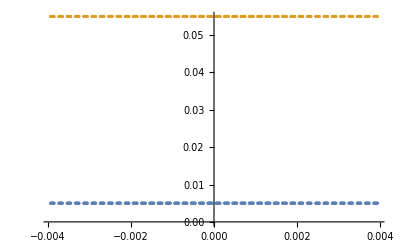

```mathematica
(* izx and ix are created here, but not yet filled with intensity values. ix will give paired values of intensity vs position in x at a particular value of z, izx stores ix for each different position z *)
izx=ConstantArray[ConstantArray[0,zpoints],xpoints];(* this is an array of 500 arrays of 500 zeros, 500 slices in the z axis of 500 intensity profiles in x (or y) *)
fmap=ConstantArray[ConstantArray[0,zpoints],Ceiling[xpoints/2]];(* the same as above, but only 250 in x (half the resolution)*)
ix=Transpose[{Xmin+(#-1) ((Xmax-Xmin)/(xpoints-1))&/@Range[xpoints],ConstantArray[0,xpoints]}]; (* a list of ordered pairs (x, 0) from xmin incremented to xmax *)
g1=Transpose[{Xmin+(#-1) ((Xmax-Xmin)/(2 xpoints-1))&/@Range[xpoints*2],ConstantArray[NaN,xpoints*2]}];(* (x, NaN) but the resolution is doubled so there's twice as many entries as above *)
g2=g1; (* g2 is another array equal to g1 *)
vis=Transpose[{(Zmin-Z1)+(#-1) ((Zmax-Zmin)/(zpoints-1))&/@Range[zpoints],ConstantArray[0,zpoints]}]; (* (z, 0) pairs same as (x, 0) pairs, ordered pairs over z range *)

f1[x_]:=If[((x>d*Round[x/d]-d*nu1/2)&&(x<d*Round[x/d]+d*nu1/2)),NaN,Z1]; (* this is a function, gives NaN if input is within d*nu1/2 of the closest int to x/d and Z1 otherwise *)
If[Z1≥Zmin && Z1≤Zmax,g1[[All,2]]=Map[f1,g1[[All,1]]]]; (* if Z1 is between Zmin and Zmax, function f1 is applied to x values in g1 and then the result is put in the second index *)
f2[x_]:=If[((x-X2>d*Round[x/d]-d*nu2/2)&&(x-X2<d*Round[x/d]+d*nu2/2)),NaN,Z2]; (* function, gives NaN if value - X2 is within a range and Z2 if out of it, similar to f1 but includes an offset *)
If[Z2≥Zmin && Z2 ≤ Zmax,g2[[All,2]]=Map[f2,g2[[All,1]]]]; (* applies f2 to g2 if Z2 is within the range *)
ListPlot[{g1,g2}] (* this should show Z1 and Z2 for a specific range of x values *)
```

### Calculating GSM parameter at first grating

```mathematica
(* refer to eqns 6, 7, 8 in McMorran thesis Appendix A 
These recalculate beam parameters according to the distance the beam has propogated and initial values *)
wz[z_,r0_,ell0_,w0_]:=w0*Abs[z/zp[z,r0]]*Sqrt[1+lambda^2 zp[z,r0]^2/(ell0^2 w0^2)];(*function to calculate GSM beam width*)
zp[z_,v_]:= (v z)/(v+z);(*Magnification factor due to wavefront curvature *) (* This one is used to simplify the other three functions *)
ellz[z_,r0_,ell0_,w0_]:=ell0*Abs[z/zp[z,r0]]*Sqrt[1+lambda^2 zp[z,r0]^2/(ell0^2 w0^2)];(*GSM coherence length*)
rz[z_,r0_,ell0_,w0_]:=z/(1-zp[z,r0]/(z*(1+lambda^2*zp[z,r0]^2/(ell0^2*w0^2))));(*radius of wavefront curvature*)
(* applies the functions above at Z1 calculated from the initial values for the beam parameters *)
r1=rz[Z1,r0,ell0,w0];
ell1=ellz[Z1,r0,ell0,w0];
w1=wz[Z1,r0,ell0,w0];
```

### Grating function 0

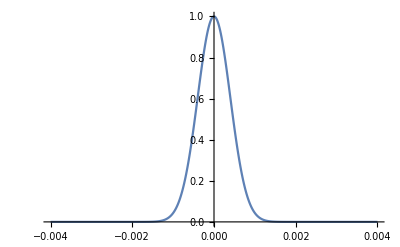

```mathematica
(* This function calculates the beam spreading as it propogates, without any effects from a grating structure *)
(* calculates w1 (beam width at given values for z, r, ell, an inital w), creates a blank ix matrix (giving intensity at specific x values), with intensity given by e^(-Pi*(x/w1)^2) (should be equal to 1 (max) at x = 0) in the second index for each pair in ix - each pair is (x, intensity at x) *)
gp0[z01_,r0_,ell0_,w0_]:=Block[
{w1=wz[z01,r0,ell0,w0],
ix=Transpose[{Xmin+(#-1) ((Xmax-Xmin)/(xpoints-1))&/@Range[xpoints],ConstantArray[0,xpoints]}]
},

ix[[All,2]]=Map[Exp[-Pi*(#/w1)^2]&,ix[[All,1]]];

Return[ix];
];
(* applies the function gp0 at location Zmin + dZ*50 (50 steps away from Zmin) *)
gp0[Zmin+dZ*50,r0,ell0,w0];
ListPlot[%, PlotRange->All, Joined->True]
```

### Grating function 1

```mathematica
(* this is similar to gp0 but models the beam after it passes through the first grating. The exact formula can be found in McMorran's thesis, Appendix A (look for the mutual intensity functions) *)
gp1[z12_,r1_,ell1_,w1_]:=Block[
{ell2=ellz[z12,r1,ell1,w1],(* beam parameters *)
w2=wz[z12,r1,ell1,w1],
r2=rz[z12,r1,ell1,w1],
ix=Transpose[{Xmin+(#-1) ((Xmax-Xmin)/(xpoints-1))&/@Range[xpoints],ConstantArray[0,xpoints]}],
cutoff=1*10^-3, (* cutoff used to round small values to 0 *)
lim=4, (* uses coefficents up to + and - limit for n and m. As n and m increase, coefficients are multiplied by a decreasing exponential so it is not necessary to cover the full range *)
dn=0,dm=0,coef=1},

Do[
dn=n-m;
dm=(m+n)/2;

(* ignoring the image charge defines coefficients using the sinc function, if not uses coefficients from ReT and ImT *)
If[ Not[image],(*If true, ignore effect of image charge*)
coef=Sinc[nu1*Pi*n]*Sinc[nu1*Pi*m]*nu1^2,coef=ReT[[x2pnt[ReT,n]]][[2]]*ReT[[x2pnt[ReT,m]]][[2]]+ImT[[x2pnt[ReT,n]]][[2]]*ImT[[x2pnt[ReT,m]]][[2]]];

coef*=Exp[-Pi*(dn*lambda*z12/(d*ell2))^2]; (* multiplies coefficients by an exponential *)

If[coef≥cutoff,ix[[All,2]]+=Map[(coef*Exp[-Pi*((#-dm*lambda*z12/d)/w2)^2]*Cos[2*Pi*(dn/d)*(#-dm*lambda*z12/d)*(1-z12/r2)])&,ix[[All,1]]];
], (* multiplies terms with coefficients larger than the cutoff by another exponential and sums them to compute intensity at each x value *)

{n,-lim,lim,1},{m,-lim,lim,1}]; (* increments n and m by one between + and - limit *)
Return[ix];
];
```

```mathematica
gp1[Z1+LT,r1,ell1,w1]; (* calculates intensity as a function of x (ix) at LT (Talbot length) beyond the first grating. You can see it spread out if you increase the distance away *)
```

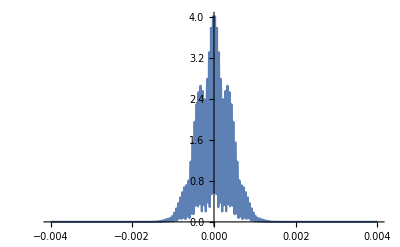

```mathematica
ListPlot[%,Joined->True, PlotRange->All]
```

### Grating function 2

```mathematica
(* similar to gp1 but this is through the second grating.
This is more complex and has addition indices because these functions come from the operation used in gp1 applied onto itself (again see McMorran's thesis for more info), and can also account for any twist between the gratings *)
(* z12 is the distance between gratings 1 and 2, z23 is the distance beyond the second, mytheta is twist between gratings *)
gp2[z12_,z23_,mytheta_,ell1x_,w1x_,r1x_,ell1y_,w1y_,r1y_,X2_]:=Block[
{theta=Pi*mytheta/180,
d1=d,
d2=d,

z13=z12+z23,
ell3x=ellz[z12+z23,r1x,ell1x,w1x],
w3x=wz[z12+z23,r1x,ell1x,w1x],
r3x=rz[z12+z23,r1x,ell1x,w1x],

ell3y=ellz[z12+z23,r1y,ell1y,w1y],
w3y=wz[z12+z23,r1y,ell1y,w1y],
r3y=rz[z12+z23,r1y,ell1y,w1y],

ix=Transpose[{Xmin+(#-1) ((Xmax-Xmin)/(xpoints-1))&/@Range[xpoints],ConstantArray[0,xpoints]}],
phix=ix,phi=0,(*phix is empty but takes the same form as ix for phi as a function of x. Phi will be calculated and phix will be filled in at each x*)
cutoff=1*10^-3, 
lim=4,
coef=1,dn=0,dm=0,m=0,n=0,a=0,b=0,c=0,d=0}, 

Do[
dn=n1-n2; 
n=(n1+n2)/2;
dm=m1-m2;
m=(m1+m2)/2;
a = x2pnt[ReT,m1]; (*a, b, c and d are used to match the indices with their locations in ReT and ImT *)
b=x2pnt[ReT,m2];
c=x2pnt[ReT,n1];
d=x2pnt[ReT,n2];


If[Not[image],(*If true, ignore effect of image charge*)
{coef=Sinc[nu1*Pi*m1]+0ⅈ,
coef*=Sinc[nu1*Pi*m2+0ⅈ]},
{coef=ReT[[a]][[2]]+ImT[[a]][[2]]ⅈ,(* full/complex form of coefficients given by adding the real and imaginary part *)
coef*=ReT[[b]][[2]]-ImT[[b]][[2]]ⅈ}]; (* multiply coefficients of m1 * coefficients of m2 *)

coef*=ReT[[c]][[2]]+ImT[[c]][[2]]ⅈ; (* same as before for n1 and n2 *)
coef*=ReT[[d]][[2]]-ImT[[d]][[2]]ⅈ;

(*Accounting for twist dependence of visibility*) 
coef*=Exp[-Pi*(dn*Sin[theta]*lambda*z23/(d2*ell3y))^2];
coef*=Exp[-Pi*(lambda*z23*(dn*Cos[theta]+dm*z13/z23)/(d1*ell3x))^2];


(*Print[ix[[All,1]]];
ix[[All,2]]+=Map[(Re[coef]*Cos[#[[2]]]-Im[coef]*Sin[#[[2]]])*Exp[-Pi*((#[[1]]-(lambda*z23/d1)*(n*Cos[theta]+m*z13/z23))/w3x)^2]&,phi];
Print[ix]*)
If[Re[coef]≥cutoff ||Im[coef]≥cutoff,(* Re[coef]/Im[coef] return the real/imaginary part of the calculated coefficients, calculates phix here and uses it in calculation of ix  *)
{
phi=dn*n*(1-z23/r3x)*Cos[theta]^2+dn*n*(1-z23/r3y)*Sin[theta]^2+dn*m*(1-z13/r3x)*Cos[theta];phi+=dm*n*(1-z13/r3x)*Cos[theta]+dm*m*(z13/z23)*(1-z13/r3x);phi*=2*Pi*lambda*z23/(d1^2);phi-=2*Pi*dn*X2/d2;phix[[All,2]]=Map[(phi-(2*Pi*#/d2)*(dn*Cos[theta]*(1-z23/r3x)+dm*(1-z13/r3x))&),phix[[All,1]]];

ix[[All,2]]+=Map[(Re[coef]*Cos[#[[2]]]-Im[coef]*Sin[#[[2]]])*Exp[-Pi*((#[[1]]-(lambda*z23/d1)*(n*Cos[theta]+m*z13/z23))/w3x)^2]&,phix]
}
]
,

{m1,-lim,lim,1},{m2,-lim,lim,1},{n1,-lim,lim,1},{n2,-lim,lim,1}];

Return[ix]];
```

#### Testing:

```mathematica
gp2[Z2-Z1,Zmin+200*dZ,theta,ell1,w1,r1,ell1,w1,r1,X2]; (* intensity at Zmin + 200*dZ beyond the second grating *)
```

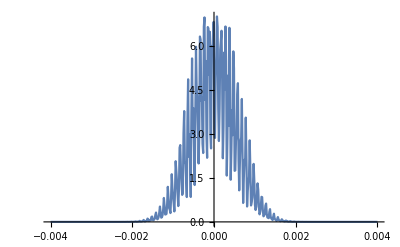

```mathematica
ListPlot[%,Joined->True,PlotRange->All]
```

```mathematica
Compute intensity at the position of 3rd grating:
```

If ShowFullPlot = False, these are the final results/ graphs

{500,2}

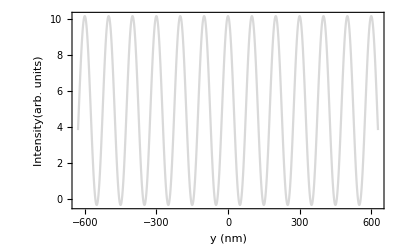

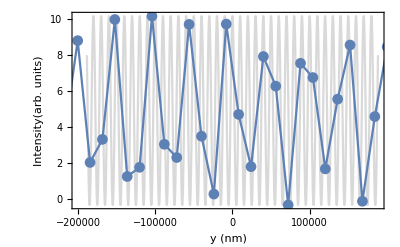

gp2 Min, Max, Contrast=

-0.354353

10.1501

1.07235

1.

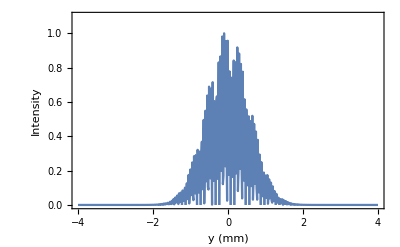

```mathematica
gp2dat=gp2[Z2-Z1,Z2-Z1,theta,ell1,w1,r1,ell1,w1,r1,X2]; (* intensity at distance beyond Z2 equal to spacing between gratings - at grating 3 *)
gp2dat[[All,1]]*=10^9; (* multiplies all x values by 10^9 (conversion from m to nm for plotting) *)
Dimensions[gp2dat] (* gives size of gp2dat*)
gp2min=Min[gp2dat[[All,2]]]; (*min intensity*)
gp2max=Max[gp2dat[[All,2]]]; (*max intensity*)
gp2mean=(gp2max+gp2min)/2; (*mean intensity*)
gp2amp=gp2max-gp2mean; (*amplitude of intensity*)
bb:=Style[#,{Bold, Larger,Black}]&; (* function, just applies a style for a graph *)
marker=Graphics[]; (*also for graphing*)
gp2dat;
Show[Plot[gp2mean+gp2amp*Sin[2* π*x/100+ π/2],{x,-200 π,200 π}(* this part is background to show diff between min and max intensity*),PlotStyle->LightGray,Frame->True,AxesOrigin->{-602,0.2}(*this is a really small portion of it, idk why*),FrameLabel->{bb@" y (nm)",bb@"Intensity(arb. units)"},TargetUnits->{1*10^-9,}],ListPlot[gp2dat,PlotMarkers->{"•",11},Joined->True] (*dots show gp2dat*)
]
(*Print["gp2 Min, Max=",MinMax[gp2dat[[All,2]]]];*)
Show[Plot[gp2mean+gp2amp*Sin[2* π*x/10000+ π/2],{x,-60000 π,60000 π (* change plot range in here *)}(* plotting again over bigger range to show the whole thing, mess with these parameters to change the sin function background *),PlotStyle->LightGray,Frame->True,AxesOrigin->{-200000,0.2} (* mess with this to change where the graph starts*),FrameLabel->{bb@" y (nm)",bb@"Intensity(arb. units)"},TargetUnits->{1*10^-9,}],ListPlot[gp2dat,PlotMarkers->{"•",11},Joined->True, PlotRange->All] (*dots show gp2dat*)
]
Text["gp2 Min, Max, Contrast="]
gp2min
gp2max
(gp2max-gp2min)/(gp2max+gp2min)

gp2dat[[All, 1]]*= 1*10^(-6); (* conversion from nm to mm *)
gp2dat[[All, 2]]/= gp2max ;(* normalization so that maximum intensity is always 1 *)
gp2max=Max[gp2dat[[All,2]]]
Show[ListPlot[gp2dat,Joined->True, PlotRange->{0,1.1}, Frame->True, FrameLabel->{bb@" y (mm)",bb@"Intensity"}]]
```

### Part 9: Compute intensity along z axis

```mathematica
(* Set ShowFullPlot to True to see this plot *)
(*this calculates ix at z positions over the full range to the third grating, uses position to determine which grating to use*)
(* constructs izx, which gives ix (intensity function along x) at each z position *)
If[ShowFullPlot,{

Do[
zpos=Zmin+i*dZ;
If[zpos>Z2,
ix=gp2[Z2-Z1,zpos-Z2,theta,ell1,w1,r1,ell1,w1,r1,X2]
,
If[zpos>Z1,
ix=gp1[zpos-Z1,r1,ell1,w1]
,
ix=gp0[zpos,r0,ell0,w0]
]
];
filter1[x_]:=If[x<0,0.,x];(*negative x values changed to 0*)
(*filter2[x_]:=If[x==NaN,0.,x];*)
ix[[All,2]]=Map[filter1,ix[[All,2]]];
(*ix[[All,2]]=Map[filter2,ix[[All,2]]];*)
ix[[All,2]]/=Max[ix[[All,2]]];
izx[[All,i+1]]=ix[[All,2]];
,
{i,0,zpoints-1,1}]

}];
```

```mathematica
(*Zoomout Plot COLORs: SunsetColors or LakeColors *)

If[ShowFullPlot, {

(* adjust scales on the axes *)
ticx = 0.1*10^-3;
ticz =  4*10^-3;
scalex = 10^-3;
scalez = 10^-3;

(* Adjust other plot parameters here, including labels, font sizes, etc*)
ListDensityPlot[ 
{izx}, ColorFunction->ColorData["SunsetColors"]  , AspectRatio->0.75,ImageSize->1200,PlotRange->All,PlotRangePadding->.001, FrameLabel->{Switch[scalez,LT ,"Z distance [Talbot length]",1,"Z distance [m]",  10^-3, "Z distance [mm]",10^-6 ,"Z distance [um]", 10^-9,"Z distance [nm]"],
Switch[scalex,d,"Y distance [slit spacing]",1,"Y distance [m]",  10^-3, "Ydistance [mm]",10^-6 ,"Y distance [um]", 10^-9,"Y distance [nm]"]},LabelStyle->(FontSize->44),
FrameTicks->{{{#,Round[(Xmin+#*dX)/scalex,0.0001] }&/@Range[0,xpoints,ticx/dX],None},{{#,NumberForm@((Zmin+#*dZ)/scalez)}&/@Range[0,zpoints,ticz/dZ],None}}]}]
```

#### Time used:

```mathematica
tafter=TimeUsed[]; (*calculating how long this part takes*)
Seconds = (tafter-tbefore); (* time in seconds *)
Minutes =(tafter-tbefore)/60; (*in minutes*)
Text["Time in seconds:"] 
Seconds
Text["Time in minutes:"] 
Minutes
```

Time in seconds:

18.671

Time in minutes:

0.311183